```mathematica
Clear["Global`*"]
```

```mathematica
(*定义常微分方程组*)
eqns={
-c *U[x]-q *U[x]^3+(3/2) q *U[x] V[x]-(q/4)* U''[x] ,
-c *V[x]+(3/4) q* V[x]^2-3 q *U[x]^2 V[x]+(3 q/4)* (U'[x])^2+(3 q/2) *U[x] U''[x]-(1/4) q *V''[x] 
}/.{U-> Function[x,a0 +a1*P[x]+b1*P[x]^(-1)], V-> Function[x,c0 +c1*P[x]+c2*P[x]^2+d1*P[x]^(-1)+d2*P[x]^(-2)]};
```

```mathematica
Clear[r0,r1,r2,r3,r4]
```

情况4
参考文献：Analytical soliton solutions for cubic-quartic perturbations of the Lakshmanan-Porsezian-Daniel equation using the modified extended tanh function method (have typo!)

Optical soliton perturbation with Kudryashov’s generalized law of refractive index and generalized nonlocal laws by improved modified extended tanh method

约束方程：

```mathematica
(*情况1(无解)： r0=r1=r3=0; *)
(*情况2(有解)： r0=r2^2/(4*r4);r1=r3=0; *)
(*情况3(无解)： r0=r1=r2=0; *)
(*情况4(有解，复杂)： r0=r1=0; *)
(*情况5(有解)： r1=r3=0; *)
r0=r1=0;
SubEqns = eqns/.{P'[x] ->Sqrt[r0+r1*P[x]+r2*P[x]^2+r3*P[x]^3 + r4*P[x]^4 ]}/.{P''[x]->(1/2)*(r1 + 2*r2*P[x] + 3*r3*P[x]^2 + 4*r4*P[x]^3)}/.{P[x]->P}
```

{-c (a0+b1/P+a1 P)-(a0+b1/P+a1 P)^3 q+3/2 (a0+b1/P+a1 P) (c0+d2/P^2+d1/P+c1 P+c2 P^2) q-1/4 q (1/2 a1 (2 P r2+3 P^2 r3+4 P^3 r4)-(b1 (2 P r2+3 P^2 r3+4 P^3 r4))/(2 P^2)+(2 b1 (P^2 r2+P^3 r3+P^4 r4))/P^3),-c (c0+d2/P^2+d1/P+c1 P+c2 P^2)-3 (a0+b1/P+a1 P)^2 (c0+d2/P^2+d1/P+c1 P+c2 P^2) q+3/4 (c0+d2/P^2+d1/P+c1 P+c2 P^2)^2 q+3/4 q (a1 √(P^2 r2+P^3 r3+P^4 r4)-(b1 √(P^2 r2+P^3 r3+P^4 r4))/P^2)^2+3/2 (a0+b1/P+a1 P) q (1/2 a1 (2 P r2+3 P^2 r3+4 P^3 r4)-(b1 (2 P r2+3 P^2 r3+4 P^3 r4))/(2 P^2)+(2 b1 (P^2 r2+P^3 r3+P^4 r4))/P^3)-1/4 q (1/2 c1 (2 P r2+3 P^2 r3+4 P^3 r4)-(d2 (2 P r2+3 P^2 r3+4 P^3 r4))/P^3-(d1 (2 P r2+3 P^2 r3+4 P^3 r4))/(2 P^2)+c2 P (2 P r2+3 P^2 r3+4 P^3 r4)+2 c2 (P^2 r2+P^3 r3+P^4 r4)+(6 d2 (P^2 r2+P^3 r3+P^4 r4))/P^4+(2 d1 (P^2 r2+P^3 r3+P^4 r4))/P^3)}

```mathematica
(*每一项乘上P四次方，变为正次的多项式*)
expandedEqns=Expand[SubEqns*P^4];
```

```mathematica
(* P 的各个次幂*)
coeffEqns=Flatten[CoefficientList[expandedEqns,P]];
(*列出方程组*)
eqnList=Thread[coeffEqns==0];
```

```mathematica
(*解代数决定方程组*)
Clear[c]
(*约束条件为：如果这几项全部都为零就排除，不显示*)
addConstraints={q!=0,AnyTrue[{a1,b1,c1,c2,d1,d2},#!=0&]};
solutionsRaw=Solve[Join[eqnList,addConstraints],{r2,r3,r4,a0,a1,b1,c0,c1,c2,d1,d2}];
solutionsRaw//Column
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{r2→-c/q,r3→0,r4→c2/2,a0→0,a1→0,b1→0,c0→0,c1→0,d1→0,d2→0}
{r2→c/q,r3→0,r4→c2/2,a0→0,a1→0,b1→0,c0→(4 c)/(3 q),c1→0,d1→0,d2→0}
{r2→-(4 c)/q,r3→2 c1,r4→0,a0→0,a1→0,b1→0,c0→0,c2→0,d1→0,d2→0}
{r2→-(4 c)/q,r3→c1,r4→-(c1^2 q)/(16 c),a0→0,a1→0,b1→0,c0→0,c2→-(c1^2 q)/(8 c),d1→0,d2→0}
{r2→(4 c)/q,r3→2 c1,r4→0,a0→0,a1→0,b1→0,c0→(4 c)/(3 q),c2→0,d1→0,d2→0}
{r2→(4 c)/q,r3→c1,r4→(c1^2 q)/(16 c),a0→0,a1→0,b1→0,c0→(4 c)/(3 q),c2→(c1^2 q)/(8 c),d1→0,d2→0}
{r2→-(4 c)/q,r3→2 c1,r4→0,a0→0,a1→0,b1→0,c0→0,c2→0,d1→0,d2→0}
{r2→(4 c)/q,r3→2 c1,r4→0,a0→0,a1→0,b1→0,c0→(4 c)/(3 q),c2→0,d1→0,d2→0}
{r2→-(4 c)/q,r3→-(8 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→0,b1→0,c0→0,c1→-(2 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→-(4 c)/q,r3→(8 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→0,b1→0,c0→0,c1→(2 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→(4 c)/q,r3→-(8 ⅈ a1 √c)/(√3 √q),r4→4 a1^2,a0→0,b1→0,c0→(4 c)/(3 q),c1→-(2 ⅈ a1 √c)/(√3 √q),c2→2 a1^2,d1→0,d2→0}
{r2→(4 c)/q,r3→(8 ⅈ a1 √c)/(√3 √q),r4→4 a1^2,a0→0,b1→0,c0→(4 c)/(3 q),c1→(2 ⅈ a1 √c)/(√3 √q),c2→2 a1^2,d1→0,d2→0}
{r2→-(4 c)/q,r3→-(4 ⅈ a1 √c)/(√q),r4→a1^2,a0→-(ⅈ √c)/(√q),b1→0,c0→0,c1→-(2 ⅈ a1 √c)/(√q),c2→a1^2,d1→0,d2→0}
{r2→-(4 c)/q,r3→-(8 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→-(ⅈ √c)/(√q),b1→0,c0→0,c1→-(2 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→-(16 c)/q,r3→-(16 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→-(ⅈ √c)/(√q),b1→0,c0→0,c1→-(4 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→-(4 c)/q,r3→(4 ⅈ a1 √c)/(√q),r4→a1^2,a0→(ⅈ √c)/(√q),b1→0,c0→0,c1→(2 ⅈ a1 √c)/(√q),c2→a1^2,d1→0,d2→0}
{r2→-(4 c)/q,r3→(8 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→(ⅈ √c)/(√q),b1→0,c0→0,c1→(2 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→-(16 c)/q,r3→(16 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→(ⅈ √c)/(√q),b1→0,c0→0,c1→(4 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→(2 (-5 c+√105 c))/(5 q),r3→(4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q),r4→4 a1^2,a0→-(ⅈ √c)/(√5 √q),b1→0,c0→(8 c)/(15 q),c1→-(ⅈ (9 √5 a1 √c-5 √21 a1 √c))/(15 √q),c2→2 a1^2,d1→0,d2→0}
{r2→-(2 (5 c+√105 c))/(5 q),r3→-(4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q),r4→4 a1^2,a0→-(ⅈ √c)/(√5 √q),b1→0,c0→(8 c)/(15 q),c1→-(ⅈ (9 √5 a1 √c+5 √21 a1 √c))/(15 √q),c2→2 a1^2,d1→0,d2→0}
{r2→(2 (-5 c+√105 c))/(5 q),r3→-(4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q),r4→4 a1^2,a0→(ⅈ √c)/(√5 √q),b1→0,c0→(8 c)/(15 q),c1→(ⅈ (9 √5 a1 √c-5 √21 a1 √c))/(15 √q),c2→2 a1^2,d1→0,d2→0}
{r2→-(2 (5 c+√105 c))/(5 q),r3→(4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q),r4→4 a1^2,a0→(ⅈ √c)/(√5 √q),b1→0,c0→(8 c)/(15 q),c1→(ⅈ (9 √5 a1 √c+5 √21 a1 √c))/(15 √q),c2→2 a1^2,d1→0,d2→0}
{r2→-c/q,r3→0,r4→c2/2,a0→0,a1→0,b1→0,c0→0,c1→0,d1→0,d2→0}
{r2→c/q,r3→0,r4→c2/2,a0→0,a1→0,b1→0,c0→(4 c)/(3 q),c1→0,d1→0,d2→0}
{r2→-(4 c)/q,r3→2 c1,r4→0,a0→0,a1→0,b1→0,c0→0,c2→0,d1→0,d2→0}
{r2→-(4 c)/q,r3→c1,r4→-(c1^2 q)/(16 c),a0→0,a1→0,b1→0,c0→0,c2→-(c1^2 q)/(8 c),d1→0,d2→0}
{r2→(4 c)/q,r3→2 c1,r4→0,a0→0,a1→0,b1→0,c0→(4 c)/(3 q),c2→0,d1→0,d2→0}
{r2→(4 c)/q,r3→c1,r4→(c1^2 q)/(16 c),a0→0,a1→0,b1→0,c0→(4 c)/(3 q),c2→(c1^2 q)/(8 c),d1→0,d2→0}

```mathematica
FullSimplify[D[Sqrt[r0+r1*P[x]+r2*P[x]^2+r3*P[x]^3 + r4*P[x]^4 ],x]/.{P'[x] ->Sqrt[r0+r1*P[x]+r2*P[x]^2+r3*P[x]^3 + r4*P[x]^4 ]}]
```

P[x] (r2+2 r4 P[x]^2)

```mathematica
(*下面要根据,r2,r4的正负+参考文献给出的结果得出p[x]表达式*)
(*通过对solutions观察，我们需要把后面几项扔了*)
(*Map[DeleteCases[#,a0->0|a1->0|b1->0]&,solutionsRaw] 不行*)
```

```mathematica
solutions = DeleteCases[solutionsRaw,_?(ContainsAll[#,{a0->0,a1->0,b1->0}]&)] ;
solutions//Column
```

{r2→-(4 c)/q,r3→-(8 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→0,b1→0,c0→0,c1→-(2 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→-(4 c)/q,r3→(8 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→0,b1→0,c0→0,c1→(2 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→(4 c)/q,r3→-(8 ⅈ a1 √c)/(√3 √q),r4→4 a1^2,a0→0,b1→0,c0→(4 c)/(3 q),c1→-(2 ⅈ a1 √c)/(√3 √q),c2→2 a1^2,d1→0,d2→0}
{r2→(4 c)/q,r3→(8 ⅈ a1 √c)/(√3 √q),r4→4 a1^2,a0→0,b1→0,c0→(4 c)/(3 q),c1→(2 ⅈ a1 √c)/(√3 √q),c2→2 a1^2,d1→0,d2→0}
{r2→-(4 c)/q,r3→-(4 ⅈ a1 √c)/(√q),r4→a1^2,a0→-(ⅈ √c)/(√q),b1→0,c0→0,c1→-(2 ⅈ a1 √c)/(√q),c2→a1^2,d1→0,d2→0}
{r2→-(4 c)/q,r3→-(8 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→-(ⅈ √c)/(√q),b1→0,c0→0,c1→-(2 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→-(16 c)/q,r3→-(16 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→-(ⅈ √c)/(√q),b1→0,c0→0,c1→-(4 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→-(4 c)/q,r3→(4 ⅈ a1 √c)/(√q),r4→a1^2,a0→(ⅈ √c)/(√q),b1→0,c0→0,c1→(2 ⅈ a1 √c)/(√q),c2→a1^2,d1→0,d2→0}
{r2→-(4 c)/q,r3→(8 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→(ⅈ √c)/(√q),b1→0,c0→0,c1→(2 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→-(16 c)/q,r3→(16 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→(ⅈ √c)/(√q),b1→0,c0→0,c1→(4 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→(2 (-5 c+√105 c))/(5 q),r3→(4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q),r4→4 a1^2,a0→-(ⅈ √c)/(√5 √q),b1→0,c0→(8 c)/(15 q),c1→-(ⅈ (9 √5 a1 √c-5 √21 a1 √c))/(15 √q),c2→2 a1^2,d1→0,d2→0}
{r2→-(2 (5 c+√105 c))/(5 q),r3→-(4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q),r4→4 a1^2,a0→-(ⅈ √c)/(√5 √q),b1→0,c0→(8 c)/(15 q),c1→-(ⅈ (9 √5 a1 √c+5 √21 a1 √c))/(15 √q),c2→2 a1^2,d1→0,d2→0}
{r2→(2 (-5 c+√105 c))/(5 q),r3→-(4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q),r4→4 a1^2,a0→(ⅈ √c)/(√5 √q),b1→0,c0→(8 c)/(15 q),c1→(ⅈ (9 √5 a1 √c-5 √21 a1 √c))/(15 √q),c2→2 a1^2,d1→0,d2→0}
{r2→-(2 (5 c+√105 c))/(5 q),r3→(4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q),r4→4 a1^2,a0→(ⅈ √c)/(√5 √q),b1→0,c0→(8 c)/(15 q),c1→(ⅈ (9 √5 a1 √c+5 √21 a1 √c))/(15 √q),c2→2 a1^2,d1→0,d2→0}

从结果上看，两组情况都会涉及到,需要a1,c不等于零
-Graphics-

```mathematica
(*Map[Assuming[a1!=0,(r3^2==4*r2*r4)/.#]&,solutions]*)
mark=Map[Refine[(r3^2==4*r2*r4)/.#,{a1!=0,c!=0}]&,solutions]
solutions1 = Pick[#,mark,True]&@solutions;
solutions2 = Pick[#,mark,False]&@solutions;
solutions1//Column
solutions2//Column
(*Select[solutions,(r3^2==4*r2*r4)/. #&]*)
```

{True,True,False,False,True,True,True,True,True,True,False,False,False,False}

{r2→-(4 c)/q,r3→-(8 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→0,b1→0,c0→0,c1→-(2 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→-(4 c)/q,r3→(8 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→0,b1→0,c0→0,c1→(2 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→-(4 c)/q,r3→-(4 ⅈ a1 √c)/(√q),r4→a1^2,a0→-(ⅈ √c)/(√q),b1→0,c0→0,c1→-(2 ⅈ a1 √c)/(√q),c2→a1^2,d1→0,d2→0}
{r2→-(4 c)/q,r3→-(8 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→-(ⅈ √c)/(√q),b1→0,c0→0,c1→-(2 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→-(16 c)/q,r3→-(16 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→-(ⅈ √c)/(√q),b1→0,c0→0,c1→-(4 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→-(4 c)/q,r3→(4 ⅈ a1 √c)/(√q),r4→a1^2,a0→(ⅈ √c)/(√q),b1→0,c0→0,c1→(2 ⅈ a1 √c)/(√q),c2→a1^2,d1→0,d2→0}
{r2→-(4 c)/q,r3→(8 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→(ⅈ √c)/(√q),b1→0,c0→0,c1→(2 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}
{r2→-(16 c)/q,r3→(16 ⅈ a1 √c)/(√q),r4→4 a1^2,a0→(ⅈ √c)/(√q),b1→0,c0→0,c1→(4 ⅈ a1 √c)/(√q),c2→2 a1^2,d1→0,d2→0}

{r2→(4 c)/q,r3→-(8 ⅈ a1 √c)/(√3 √q),r4→4 a1^2,a0→0,b1→0,c0→(4 c)/(3 q),c1→-(2 ⅈ a1 √c)/(√3 √q),c2→2 a1^2,d1→0,d2→0}
{r2→(4 c)/q,r3→(8 ⅈ a1 √c)/(√3 √q),r4→4 a1^2,a0→0,b1→0,c0→(4 c)/(3 q),c1→(2 ⅈ a1 √c)/(√3 √q),c2→2 a1^2,d1→0,d2→0}
{r2→(2 (-5 c+√105 c))/(5 q),r3→(4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q),r4→4 a1^2,a0→-(ⅈ √c)/(√5 √q),b1→0,c0→(8 c)/(15 q),c1→-(ⅈ (9 √5 a1 √c-5 √21 a1 √c))/(15 √q),c2→2 a1^2,d1→0,d2→0}
{r2→-(2 (5 c+√105 c))/(5 q),r3→-(4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q),r4→4 a1^2,a0→-(ⅈ √c)/(√5 √q),b1→0,c0→(8 c)/(15 q),c1→-(ⅈ (9 √5 a1 √c+5 √21 a1 √c))/(15 √q),c2→2 a1^2,d1→0,d2→0}
{r2→(2 (-5 c+√105 c))/(5 q),r3→-(4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q),r4→4 a1^2,a0→(ⅈ √c)/(√5 √q),b1→0,c0→(8 c)/(15 q),c1→(ⅈ (9 √5 a1 √c-5 √21 a1 √c))/(15 √q),c2→2 a1^2,d1→0,d2→0}
{r2→-(2 (5 c+√105 c))/(5 q),r3→(4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q),r4→4 a1^2,a0→(ⅈ √c)/(√5 √q),b1→0,c0→(8 c)/(15 q),c1→(ⅈ (9 √5 a1 √c+5 √21 a1 √c))/(15 √q),c2→2 a1^2,d1→0,d2→0}

两组中只用其中一种情况，另一个类似，但是第二组需要有另一种情况，不讨论了，太多了

```mathematica
(*最简单情况，c，q都大于零*)
Clear[v,u]
```

约束方程解的处理 c>0, q<0

```mathematica
odeList =P[z]->(-r2(Tanh[1/2*√r2*z]+1))/r3/.solutions1;
r2Pos = (r2 Sech[1/2 √r2*z]^2)/(2 √(r2*r4)Tanh[1/2 √r2*z]-r3);r2Neg =  -(r2 Sec[1/2 √-r2*z]^2)/(2 √(-r2*r4)Tan[1/2 √-r2*z]+r3);
odeList2 = Map[
If[
Simplify[r2 >0/. #, c>0&&q <0],
P[z]->r2Pos/.#, P[z]-> r2Neg/.#]&,
solutions2
];
```

验证的为第一分类解

```mathematica
(*原始偏微分方程*)
Peqns={D[u[x,t],t]-3 q u[x,t]^2 D[u[x,t],x]+(3/2) q D[(u[x,t] v[x,t]),x]-(1/4) q D[u[x,t],{x,3}]==0,D[v[x,t],t]+(3/2) q v[x,t] D[v[x,t],x]-3 q D[(u[x,t]^2 v[x,t]),x]+3 q D[u[x,t],x] D[u[x,t],{x,2}]+(3/2) q u[x,t] D[u[x,t],{x,3}]-(1/4) q D[v[x,t],{x,3}]==0};
```

```mathematica
(*验证一组解*)
Peqns/. {solU/.odeList[[4]]/.solutions1[[4]]/.z->(x-c*t),solV/.odeList[[4]]/.solutions1[[4]]/.z->(x-c*t)

}//FullSimplify
```

{True,True}

情况1的验证

```mathematica
solUsp = u->a0 +a1*P[z]+b1*P[z]^(-1);
solVsp = v->c0 +c1*P[z]+c2*P[z]^2+d1*P[z]^(-1)+d2*P[z]^(-2);
c1usol= MapThread[(solUsp/. #1/. #2/. z->(x-c*t))&,{solutions1,odeList}];
c1vsol = MapThread[(solVsp/. #1/. #2/. z->(x-c*t))&,{solutions1,odeList}];
Map[
(Peqns/. 
{u->Function[{x,t},c1usol[[#]]],
v->Function[{x,t},c1vsol[[#]]]
}
)&,{Table[i,{i,Length[c1usol]}]}
]
```

{{{0,0,0,0,0,0,0,0}==0,{0,0,0,0,0,0,0,0}==0}}

情况2的解

```mathematica
c2usol = MapThread[(solUsp/. #1/. #2/. z->(x-c*t))&,{solutions2,odeList2}];
c2vsol = MapThread[(solVsp/. #1/. #2/. z->(x-c*t))&,{solutions2,odeList2}];
```

情况1 的验证

```mathematica
allK = r2/.solutions1
```

{-(4 c)/q,-(4 c)/q,-(4 c)/q,-(4 c)/q,-(16 c)/q,-(4 c)/q,-(4 c)/q,-(16 c)/q}

```mathematica
(*https://mathematica.stackexchange.com/questions/132191/how-to-combine-lists*)
Grid[Transpose[{c1usol,c1vsol}]]
```

u→(ⅈ √c (1+Tanh[√(-c/q) (-c t+x)]))/(2 √q) | v→(c (1+Tanh[√(-c/q) (-c t+x)]))/q-(c (1+Tanh[√(-c/q) (-c t+x)])^2)/(2 q)
u→-(ⅈ √c (1+Tanh[√(-c/q) (-c t+x)]))/(2 √q) | v→(c (1+Tanh[√(-c/q) (-c t+x)]))/q-(c (1+Tanh[√(-c/q) (-c t+x)])^2)/(2 q)
u→-(ⅈ √c)/(√q)+(ⅈ √c (1+Tanh[√(-c/q) (-c t+x)]))/(√q) | v→(2 c (1+Tanh[√(-c/q) (-c t+x)]))/q-(c (1+Tanh[√(-c/q) (-c t+x)])^2)/q
u→-(ⅈ √c)/(√q)+(ⅈ √c (1+Tanh[√(-c/q) (-c t+x)]))/(2 √q) | v→(c (1+Tanh[√(-c/q) (-c t+x)]))/q-(c (1+Tanh[√(-c/q) (-c t+x)])^2)/(2 q)
u→-(ⅈ √c)/(√q)+(ⅈ √c (1+Tanh[2 √(-c/q) (-c t+x)]))/(√q) | v→(4 c (1+Tanh[2 √(-c/q) (-c t+x)]))/q-(2 c (1+Tanh[2 √(-c/q) (-c t+x)])^2)/q
u→(ⅈ √c)/(√q)-(ⅈ √c (1+Tanh[√(-c/q) (-c t+x)]))/(√q) | v→(2 c (1+Tanh[√(-c/q) (-c t+x)]))/q-(c (1+Tanh[√(-c/q) (-c t+x)])^2)/q
u→(ⅈ √c)/(√q)-(ⅈ √c (1+Tanh[√(-c/q) (-c t+x)]))/(2 √q) | v→(c (1+Tanh[√(-c/q) (-c t+x)]))/q-(c (1+Tanh[√(-c/q) (-c t+x)])^2)/(2 q)
u→(ⅈ √c)/(√q)-(ⅈ √c (1+Tanh[2 √(-c/q) (-c t+x)]))/(√q) | v→(4 c (1+Tanh[2 √(-c/q) (-c t+x)]))/q-(2 c (1+Tanh[2 √(-c/q) (-c t+x)])^2)/q

为了r2>0,则c>0,q<0解形式差不多列一个

```mathematica
Grid[Transpose[{c2usol,c2vsol}]]
```

u→-(4 a1 c Sec[√(-c/q) (-c t+x)]^2)/(q (-(8 ⅈ a1 √c)/(√3 √q)+8 √(-(a1^2 c)/q) Tan[√(-c/q) (-c t+x)])) | v→(4 c)/(3 q)+(32 a1^2 c^2 Sec[√(-c/q) (-c t+x)]^4)/(q^2 (-(8 ⅈ a1 √c)/(√3 √q)+8 √(-(a1^2 c)/q) Tan[√(-c/q) (-c t+x)])^2)+(8 ⅈ a1 c^(3/2) Sec[√(-c/q) (-c t+x)]^2)/(√3 q^(3/2) (-(8 ⅈ a1 √c)/(√3 √q)+8 √(-(a1^2 c)/q) Tan[√(-c/q) (-c t+x)]))
u→-(4 a1 c Sec[√(-c/q) (-c t+x)]^2)/(q ((8 ⅈ a1 √c)/(√3 √q)+8 √(-(a1^2 c)/q) Tan[√(-c/q) (-c t+x)])) | v→(4 c)/(3 q)+(32 a1^2 c^2 Sec[√(-c/q) (-c t+x)]^4)/(q^2 ((8 ⅈ a1 √c)/(√3 √q)+8 √(-(a1^2 c)/q) Tan[√(-c/q) (-c t+x)])^2)-(8 ⅈ a1 c^(3/2) Sec[√(-c/q) (-c t+x)]^2)/(√3 q^(3/2) ((8 ⅈ a1 √c)/(√3 √q)+8 √(-(a1^2 c)/q) Tan[√(-c/q) (-c t+x)]))
u→-(ⅈ √c)/(√5 √q)-(2 a1 (-5 c+√105 c) Sec[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(5 q ((4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (-5 c+√105 c))/q) Tan[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)])) | v→(8 c)/(15 q)+(8 a1^2 (-5 c+√105 c)^2 Sec[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]^4)/(25 q^2 ((4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (-5 c+√105 c))/q) Tan[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)])^2)+(2 ⅈ (9 √5 a1 √c-5 √21 a1 √c) (-5 c+√105 c) Sec[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(75 q^(3/2) ((4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (-5 c+√105 c))/q) Tan[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]))
u→-(ⅈ √c)/(√5 √q)-(2 a1 (5 c+√105 c) Sech[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(5 q ((4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (5 c+√105 c))/q) Tanh[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)])) | v→(8 c)/(15 q)+(8 a1^2 (5 c+√105 c)^2 Sech[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]^4)/(25 q^2 ((4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (5 c+√105 c))/q) Tanh[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)])^2)+(2 ⅈ (9 √5 a1 √c+5 √21 a1 √c) (5 c+√105 c) Sech[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(75 q^(3/2) ((4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (5 c+√105 c))/q) Tanh[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]))
u→(ⅈ √c)/(√5 √q)-(2 a1 (-5 c+√105 c) Sec[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(5 q (-(4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (-5 c+√105 c))/q) Tan[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)])) | v→(8 c)/(15 q)+(8 a1^2 (-5 c+√105 c)^2 Sec[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]^4)/(25 q^2 (-(4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (-5 c+√105 c))/q) Tan[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)])^2)-(2 ⅈ (9 √5 a1 √c-5 √21 a1 √c) (-5 c+√105 c) Sec[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(75 q^(3/2) (-(4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (-5 c+√105 c))/q) Tan[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]))
u→(ⅈ √c)/(√5 √q)-(2 a1 (5 c+√105 c) Sech[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(5 q (-(4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (5 c+√105 c))/q) Tanh[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)])) | v→(8 c)/(15 q)+(8 a1^2 (5 c+√105 c)^2 Sech[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]^4)/(25 q^2 (-(4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (5 c+√105 c))/q) Tanh[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)])^2)-(2 ⅈ (9 √5 a1 √c+5 √21 a1 √c) (5 c+√105 c) Sech[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(75 q^(3/2) (-(4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (5 c+√105 c))/q) Tanh[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]))

Singular solition solution -(4 a1 c Sec[√(-c/q) (-c t+x)]^2)/(q ((8 ⅈ a1 √c)/(√3 √q)+8 √(-(a1^2 c)/q) Tan[√(-c/q) (-c t+x)]))  c=2;q=-1;a1=1;
非连续 (ⅈ √c)/(√q)-(ⅈ √c (1+Tanh[2 √(-c/q) (-c t+x)]))/(√q) c=1;q=-30;a1 = 1; (调范围会出现奇点，没明白)

-Graphics3D-

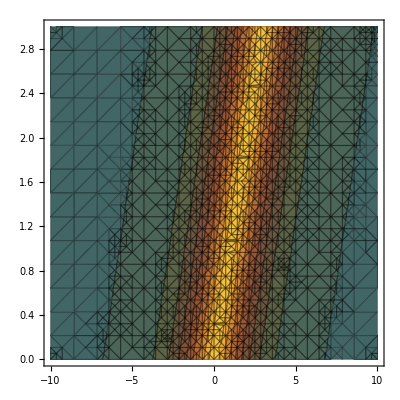

```mathematica
c=1;q=-30;a1=1;

setting1={ClippingStyle->None,
(*Exclusions->"Singularities",*)
Exclusions->"Singularities",
AxesLabel->Automatic,
Boxed->False,
PlotRange->Automatic,
ColorFunction->(ColorData["FallColors"][#2]&),PlotPoints->60(* 60很顺滑*)

};
f[x_,t_]:=(ⅈ √c)/(√q)-(ⅈ √c (1+Tanh[2 √(-c/q) (-c t+x)]))/(√q)//N 
Plot3D[-Abs[f[x,t]],{x,-10,10},{t,0,3},Evaluate[setting1],ColorFunction->Function[{x,t,z},ColorData["LakeColors"][z]],AxesLabel->{"x","t","U"," "},PlotLabel->"U"]
ContourPlot[-Abs[f[x,t]],{x,-10,10},{t,0,3},Mesh->All,ColorFunction->"FallColors"]
(*Plot3D[f[x,t],{x,-2,2},{t,0.1,1},Evaluate[setting1],ColorFunction->Function[{x,t,z},ColorData["LakeColors"][z]],AxesLabel->{"x","t","U"," "},PlotLabel->"U"]
*)
(*Plot3D[Abs[f[x,t]],{x,-20,20},{t,0,3},PlotRange->Automatic(*,PlotPoints->90*),AxesLabel->Automatic,Boxed->False,ColorFunction->(ColorData["FallColors"][#2]&)]*)
```

```mathematica
Clear[q,c]
```

```mathematica
(ⅈ √c)/(√5 √q)-(2 a1 (-5 c+√105 c) Sec[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(5 q (-(4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (-5 c+√105 c))/q) Tan[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]))//N
```

(2.23607+0. ⅈ)+(52.4695 Sec[3.62179 (-2.5 t+x)]^2)/((-3.71769+0. ⅈ)+28.9743 Tan[3.62179 (-2.5 t+x)])